```mathematica
(*1. Selected project, created a directory and submited it to github.*)
```

```mathematica
(* 2. Introduction
(a) The syntax of the Mathematica language *)
```

```mathematica
{FullForm[a*b+c],FullForm[a+b*c]}
```

{Plus[Times[a,b],c],Plus[a,Times[b,c]]}

```mathematica
a*b+c//f
```

f[a b+c]

```mathematica
f@a*b+c
```

c+b f[a]

```mathematica
FullForm[a*(b+c)]
```

Times[a,Plus[b,c]]

```mathematica
∀_x∃_y x⊗y>y∧m ≠0⇒n⩾̸m
```

∀_x∃_y x⊗y>y&&m≠0⇒n⩾̸m

```mathematica
FullForm[%]
```

And[ForAll[x,Exists[y,Greater[CircleTimes[x,y],y]]],DoubleRightArrow[Unequal[m,0],NotGreaterSlantEqual[n,m]]]

```mathematica
{x -> #^2 &, (x -> #^2)&, x -> (#^2&)}
```

{x→#1^2&,x→#1^2&,x→(#1^2&)}

```mathematica
FullForm[a+b+c+d]
```

Plus[a,b,c,d]

```mathematica
FullForm[a^b^c^d]
```

Power[a,Power[b,Power[c,d]]]

```mathematica
a⊕b⊕c//FullForm
```

CirclePlus[a,b,c]

```mathematica
a×a×a×b×b×c
```

a^3 b^2 c

```mathematica
∫k[x]ⅆx//FullForm
```

Integrate[k[x],x]

```mathematica
∫a[x]b[x]ⅆx +c[x]
```

c[x]+∫a[x] b[x]ⅆx

```mathematica
x^(a+b)
```

x^(a+b)

```mathematica
D[x^n, x]
```

n x^(-1+n)

```mathematica
∑_(n=1)^∞ 1/n^s
```

Zeta[s]

```mathematica
∑_(n=1)^∞ 1/n^s+n
```

n+Zeta[s]

```mathematica
(*(b)The meaning of Expressions*)
```

```mathematica
(*meaning of             f meaning ofx,y...                 examples
Function                arguments or parameters              Sin[x],f[x,y]
Command                  arguments or parameters            Expand[(x+1)^2]
Operator                  operands                            x+y,a=b
Head                        elements                         {a,b,c}
Objecttype                  contents                      RGBColor[r,g,b]*)
```

```mathematica
(*(c)The Four Kinds of Bracketing in Mathematica*)
```

```mathematica
(*(term) parentheses for grouping
   f[x] square brackets for functions
  {a,b,c} curly braces for lists
  v[[i]] double brackets for indexing (Part[v,i])
 When the expressions you type in are complicated,it is often a good idea to put extra space inside each set of brackets.This makes it somewhat easier for you to see matching pairs of brackets.*)
```

```mathematica
(*(d) Use Brackets and Braces Correctly: *)
(*You use parentheses in Mathematica for grouping expressions and to determine the precedence of operations:*)
1+2/3
```

5/3

```mathematica
(1+2)/3
```

1

```mathematica
(*A list in Mathematica is represented by braces and is a collection of items referred to as elements.*)
(*Create a List of the first five positive integers:*)
{1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
{1,b,2,3,3x==12,√(9+y),"hello"}
```

```mathematica
{1,b,2,3,3 x==12,√(9+y),"hello"}
(*Lists can contain other lists to create nested lists:*)
{1,1,{3,4,5},{3,2}}
```

{1,b,2,3,3 x==12,√(9+y),hello}

{1,1,{3,4,5},{3,2}}

```mathematica
(*Square brackets are used in Mathematica to enclose the arguments of functions.*)
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Sin[2]
```

Sin[2]

```mathematica
N[Sin[2]]
```

0.909297

```mathematica
(*Mathematica uses double square brackets as the short form for the Part function,which is used to get parts of lists:*)
v=Range[10]^2
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
v[[3]]
```

9

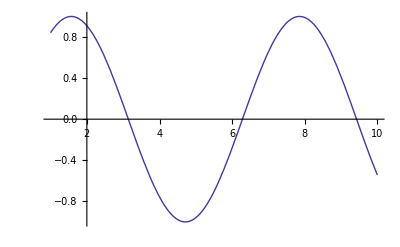

```mathematica
Plot[Sin[x],{x,1,10}]
```

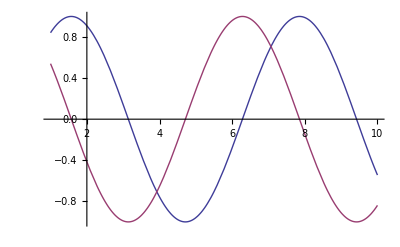

```mathematica
Plot[{Sin[x],Cos[x]},{x,1,10}]
```

```mathematica
(*All bracketing characters must be balanced for Mathematica to evaluate an expression.When a bracketing character is unbalanced,the Mathematica front end colors it purple and attempting to evaluate the expression produces an error*)
```

```mathematica
(* 3. Symbolic Analysis *)
(*(a) Symbolic Computation:*)
```

```mathematica
3+62-1
```

64

```mathematica
3x-x+2
```

2+2 x

```mathematica
-1+2x+x^3
```

-1+2 x+x^3

```mathematica
x^2+x-4x^2
```

x-3 x^2

```mathematica
(*Mathematica rearranges and combines terms using the standard rules of algebra.*)
x y+2x^2y+y^2 x^2 - 2 y x
```

-x y+2 x^2 y+x^2 y^2

```mathematica
(x + 2 y +1)(x - 2)^2
```

```mathematica
(-2+x)^2 (1+x+2 y)
```

(-2+x)^2 (1+x+2 y)

```mathematica
(* Expand multiplies ou product and powers.*)
```

```mathematica
Expand[%]
(*Factor does the inverse of Expand*)
```

4-3 x^2+x^3+8 y-8 x y+2 x^2 y

```mathematica
Factor[%]
```

(-2+x)^2 (1+x+2 y)

```mathematica
Sqrt[2]/9801(4 n)!(1103 + 26390 n )/ (n! ^4 396^(4n))
```

(2^(1/2-8 n) 99^(-2-4 n) (1103+26390 n) (4 n)!)/(n!)^4

```mathematica
Sqrt[1 + x]^4
```

(1+x)^2

```mathematica
Log[1 + Cos[x]]
```

Log[1+Cos[x]]

```mathematica
(*(b) Values for Symbols"*)
1+2 x/.x->3
```

7

```mathematica
(* You can replace x with any expression. *)
1+x+x^2/.x->2-y
```

3+(2-y)^2-y

```mathematica
x -> 3+y
```

x→3+y

```mathematica
x^2-9/.%
```

-9+(3+y)^2

```mathematica
(x+y) (x-y)^2/.{x->3,y->1-a}
```

(4-a) (2+a)^2

```mathematica
(*The replacement operator allows you to apply transformation rules to a particular expression.Sometimes,however,you will want to define transformation rules that should always be applied.For example,you might want to replace with whenever occurs.As discussed in "Defining Variables",you can do this by assigning the value to using.Once you have made the assignment,will always be replaced by,whenever it appears.*)
x = 3
```

3

```mathematica
x^2-1
```

8

```mathematica
x=1 +a
```

1+a

```mathematica
x^2-1
```

-1+(1+a)^2

```mathematica
x+5 -2x
```

6+a-2 (1+a)

```mathematica
(*Removes the value you assigned to x.*)
x=.
```

```mathematica
x+5-2x
```

5-x

```mathematica
t = 1 + x^2
```

1+x^2

```mathematica
(*This finds the value of,and then replaces by in it.*)
```

```mathematica
t/.x->2
```

5

```mathematica
t/.x->5 a
```

1+25 a^2

```mathematica
(*Finds the value of t when x is replaced by Pi, and then evaluates the result numerically*)
```

```mathematica
t/.x->Pi//N
```

10.8696

```mathematica
(*(c) Transforming Algebraic Expressions: *)
Expand[(1+x)^2]
```

1+2 x+x^2

```mathematica
(*Factor recovers the original form. *)
```

```mathematica
Factor[%]
```

(1+x)^2

```mathematica
Expand[(1+x+3 y)^4]
```

1+4 x+6 x^2+4 x^3+x^4+12 y+36 x y+36 x^2 y+12 x^3 y+54 y^2+108 x y^2+54 x^2 y^2+108 y^3+108 x y^3+81 y^4

```mathematica
Factor[%]
```

(1+x+3 y)^4

```mathematica
Factor[x^10 - 1]
```

(-1+x) (1+x) (1-x+x^2-x^3+x^4) (1+x+x^2+x^3+x^4)

```mathematica
Expand[%]
```

-1+x^10

```mathematica
(*(d)Simplifying Algebraic Expressions: *)
```

```mathematica
(*Simplify[expr] try to find the simplest form of expr by applying various standard algebraic transformations
FullSimplify[expr] try to find the simplest form by applying a wide range of transformations*)
```

```mathematica
Simplify[x^2 + 2 x +1]
```

(1+x)^2

```mathematica
Simplify[ x^10 -1]
```

-1+x^10

```mathematica
Integrate[1/(x^4 - 1),x]
```

-ArcTan[x]/2+1/4 Log[1-x]-1/4 Log[1+x]

```mathematica
D[%,x]
```

-1/(4 (1-x))-1/(4 (1+x))-1/(2 (1+x^2))

```mathematica
Simplify[%]
```

1/(-1+x^4)

```mathematica
Simplify[Gamma[x]Gamma[1-x]]
```

Gamma[1-x] Gamma[x]

```mathematica
FullSimplify[Gamma[x]Gamma[1-x]]
```

π Csc[π x]

```mathematica
(*For fairly small expressions,FullSimplify will often succeed in making some remarkable simplifications.But for larger expressions,it can become unmanageably slow.The reason for this is that to do its job,FullSimplify effectively has to try combining every part of an expression with every other,and for large expressions the number of cases that it has to consider can be astronomically large.Simplify also has a difficult task to do,but it is set up to avoid some of the most time-consuming transformations that are tried by FullSimplify.For simple algebraic calculations,therefore,you may often find it convenient to apply Simplify quite routinely to your results.*)
```

```mathematica
(*4.Calculus*)
(* (a) Differentiation: *)
```

```mathematica
(*D[f,x] partial derivative
D[f,x,y,...] multiple derivative
D[f,{x,n}] nth derivative
D[f,x,NonConstants->{v1,v2,...}] with the taken to depend on x*)
```

```mathematica
D[x^n,x]
```

n x^(-1+n)

```mathematica
(*This gives the third derivative*)
```

```mathematica
D[x^n,{x,3}]
```

(-2+n) (-1+n) n x^(-3+n)

```mathematica
D[x[1]^2+x[2]^2,x[1]]
```

2 x[1]

```mathematica
(*D does the partial differentiation. It assumes here that y is independent of x*)
D[x^2 + y^2,x]
```

2 x

```mathematica
D[x^2 + y[x]^2,x]
```

2 x+2 y[x] y'[x]

```mathematica
D[x^2 + y^2,x,NonConstants ->{y}]
```

2 x+2 y D[y,x,NonConstants→{y}]

```mathematica
D[x^2 + y^2,{{x,y}}]
```

{2 x,2 y}

```mathematica
D[x^2 + y^2,{{x,y},2}]
```

{{2,0},{0,2}}

```mathematica
(*This gives the Jacobian for a vector function.*)
```

```mathematica
D[{x^2 + y^2,x y},{{x,y}}]
```

{{2 x,2 y},{y,x}}

```mathematica
(*(b) Integration *)
```

```mathematica
Integrate[x^n,x]
```

x^(1+n)/(1+n)

```mathematica
Integrate[ 1 / (x^4 - a^4), x]
```

-ArcTan[x/a]/(2 a^3)+Log[a-x]/(4 a^3)-Log[a+x]/(4 a^3)

```mathematica
Integrate[Log[1 -x^2],x]
```

-2 x-Log[1-x]+Log[1+x]+x Log[1-x^2]

```mathematica
Integrate[Log[1 - x^2]/x,x]
```

-1/2 PolyLog[2,x^2]

```mathematica
Integrate[Exp[1-x^2],x]
```

1/2 ⅇ √π Erf[x]

```mathematica
(*This one involves a Fresnel Function*)
```

```mathematica
Integrate[Sin[x^2],x]
```

√(π/2) FresnelS[√(2/π) x]

```mathematica
(*Requires a hypergeometric function*)
```

```mathematica
Integrate[(1 - x^2)^n, x]
```

x Hypergeometric2F1[1/2,-n,3/2,x^2]

```mathematica
Integrate[x^x,x]
```

∫x^x ⅆx

```mathematica
Integrate[Sin[x]^2,{x,a,v=b}]
```

1/2 (-a+b+Cos[a] Sin[a]-Cos[b] Sin[b])

```mathematica
Integrate[Exp[-x^2],{x,0,Infinity}]
```

(√π)/2

```mathematica
Integrate[x^x,{x,0,1}]
```

∫_0^1 x^x ⅆx

```mathematica
N[%]
```

0.783431

```mathematica
Integrate[x^2 + y^2,{x,0,1},{y,0,x}]
```

1/3

```mathematica
Integrate[x^10Boole[x^2 + y^2 ≤1],{x,-1,1},{y,-1,1}]
```

(21 π)/512

```mathematica
(*(c)Indefinite Integrals:*)
```

```mathematica
Integrate[x^2,x]
```

x^3/3

```mathematica
D[%+c,x]
```

x^2

```mathematica
Integrate[1/(x^2 - 1),x]
```

1/2 Log[1-x]-1/2 Log[1+x]

```mathematica
D[%,x]
```

-1/(2 (1-x))-1/(2 (1+x))

```mathematica
Simplify[%]
```

1/(-1+x^2)

```mathematica
Integrate[a x^2,x]
```

(a x^3)/3

```mathematica
Integrate[x b[x]^2,b[x]]
```

1/3 x b[x]^3

```mathematica
Integrate[x^n,x]
```

x^(1+n)/(1+n)

```mathematica
Integrate[x^-1,x]
```

Log[x]

```mathematica
(*You should realize that the result for any particular integral can often be written in many different forms.Mathematica tries to give you the most convenient form,following principles such as avoiding explicit complex numbers unless your input already contains them.*)
```

```mathematica
Integrate[1/(1+ a x^2),x]
```

ArcTan[√a x]/(√a)

```mathematica
Integrate[1/(1 -b x^2),x]
```

ArcTanh[√b x]/(√b)

```mathematica
%/.b->-a
```

ArcTanh[√-a x]/(√-a)

```mathematica
D[%,x]
```

1/(1+a x^2)

```mathematica
Simplify[D[{ArcTan[x],-ArcTan[1/x]},x]]
```

{1/(1+x^2),1/(1+x^2)}

```mathematica
Integrate[1/(1 + x^2),x]
```

ArcTan[x]

```mathematica
(*(d)Differential Equations:*)
```

```mathematica
DSolve[y'[x] + y[x] == 1,y[x],x]
```

{{y[x]→1+ⅇ^-x C[1]}}

```mathematica
y[x]+2 y'[x]+y[0]/.%
```

{1+ⅇ^-x C[1]+y[0]+2 y'[x]}

```mathematica
DSolve[y'[x] + y[x] == 1, y, x]
```

{{y→Function[{x},1+ⅇ^-x C[1]]}}

```mathematica
y[x]+2 y'[x]+y[0]/.%
```

{2+C[1]-ⅇ^-x C[1]}

```mathematica
y'[x]+y[x]==1/.%%
```

{True}

```mathematica
DSolve[{y[x] == -z'[x],z[x] == -y'[x]},{y,z},x]
```

{{y→Function[{x},1/2 ⅇ^-x (1+ⅇ^(2 x)) C[1]-1/2 ⅇ^-x (-1+ⅇ^(2 x)) C[2]],z→Function[{x},-1/2 ⅇ^-x (-1+ⅇ^(2 x)) C[1]+1/2 ⅇ^-x (1+ⅇ^(2 x)) C[2]]}}

```mathematica
DSolve[y[x]y'[x] == 1, y , x]
```

{{y→Function[{x},-√2 √(x+C[1])]},{y→Function[{x},√2 √(x+C[1])]}}

```mathematica
(*You can add constraints and boundary conditions for differential equations by explicitly giving additional equations*)
```

```mathematica
DSolve[{y'[x] == a y[x], y[0] == 1}, y[x] ,x]
```

{{y[x]→ⅇ^(a x)}}

```mathematica
DSolve[y''''[x] == y[x], y[x] ,x]
```

{{y[x]→ⅇ^x C[1]+ⅇ^-x C[3]+C[2] Cos[x]+C[4] Sin[x]}}

```mathematica
DSolve[{y''''[x] == y[x],y[0] == y'[0] == 0},y[x],x]
```

{{y[x]→ⅇ^-x (-C[1]+ⅇ^(2 x) C[1]-C[2]+ⅇ^x C[2] Cos[x]-2 ⅇ^x C[1] Sin[x]-ⅇ^x C[2] Sin[x])}}

```mathematica
DSolve[y'[x] - x y[x] == 0, y[x] ,x]
```

{{y[x]→ⅇ^(x^2/2) C[1]}}

```mathematica
DSolve[y'[x] - x y[x] == 1,y[x],x]
```

{{y[x]→ⅇ^(x^2/2) C[1]+ⅇ^(x^2/2) √(π/2) Erf[x/(√2)]}}

```mathematica
DSolve[y''[x] - x y[x] == 0,y[x],x]
```

{{y[x]→AiryAi[x] C[1]+AiryBi[x] C[2]}}

```mathematica
DSolve[y''[x] - Exp[x]y[x] == 0,y[x],x]
```

{{y[x]→BesselI[0,2 √(ⅇ^x)] C[1]+2 BesselK[0,2 √(ⅇ^x)] C[2]}}

```mathematica
(*This Requires Mathieu functions.*)
```

```mathematica
DSolve[y''[x] + Cos[x]y[x] == 0,y ,x]
```

{{y→Function[{x},C[1] MathieuC[0,-2,x/2]+C[2] MathieuS[0,-2,x/2]]}}

```mathematica
(*And this Legendre Functions.*)
DSolve[y''[x]- Cot[x]^2 y[x] == 0,y[x],x]
```

{{y[x]→C[1] (-1+Cos[x]^2)^(1/4) LegendreP[1/2,(√5)/2,Cos[x]]+C[2] (-1+Cos[x]^2)^(1/4) LegendreQ[1/2,(√5)/2,Cos[x]]}}

```mathematica
DSolve[x^2 y''[x] + y[x] == 0,y[x],x]
```

{{y[x]→√x C[1] Cos[1/2 √3 Log[x]]+√x C[2] Sin[1/2 √3 Log[x]]}}

```mathematica
DSolve[y'''[x] + x y[x] == 0,y[x], x]
```

{{y[x]→C[1] HypergeometricPFQ[{},{1/2,3/4},-x^4/64]+(x C[2] HypergeometricPFQ[{},{3/4,5/4},-x^4/64])/(2 √2)+1/8 x^2 C[3] HypergeometricPFQ[{},{5/4,3/2},-x^4/64]}}

```mathematica
DSolve[y'''[x]+Exp[x]y[x] == 0,y[x],x]
```

{{y[x]→C[1] HypergeometricPFQ[{},{1,1},-ⅇ^x]+C[2] MeijerG[{{},{}},{{0,0},{0}},-ⅇ^x]+C[3] MeijerG[{{},{}},{{0,0,0},{}},ⅇ^x]}}

```mathematica
DSolve[y'[x] - y[x]^2 == 0,y[x],x]
```

{{y[x]→1/(-x-C[1])}}

```mathematica
DSolve[y'[x] -y[x]^2 == x,y[x],x]//FullSimplify
```

{{y[x]→(√x (-BesselJ[-2/3,(2 x^(3/2))/3]+BesselJ[2/3,(2 x^(3/2))/3] C[1]))/(BesselJ[1/3,(2 x^(3/2))/3]+BesselJ[-1/3,(2 x^(3/2))/3] C[1])}}

```mathematica
(*Bernoulli equation*)
```

```mathematica
DSolve[y'[x] - x y[x]^2 -y[x] == 0,y[x],x]
```

{{y[x]→-ⅇ^x/(-ⅇ^x+ⅇ^x x-C[1])}}

```mathematica
DSolve[y'[x]- x y[x]^3 +y[x] == 0,y[x],x]
```

{{y[x]→-(√2)/(√(1+2 x+2 ⅇ^(2 x) C[1]))},{y[x]→(√2)/(√(1+2 x+2 ⅇ^(2 x) C[1]))}}

```mathematica
(*This Abel equation can be solved, but only implicitly*)
```

```mathematica
DSolve[y'[x] + x y[x]^3 +y[x]^2 == 0,y[x],x]
```

Solve[1/2 ((2 ArcTanh[(-1-2 x y[x])/(√5)])/(√5)+Log[(-1-x y[x] (-1-x y[x]))/(x^2 y[x]^2)])==C[1]-Log[x],y[x]]

```mathematica
DSolve[y'[x] -y[x] == UnitStep[x],y[x],x]
```

{{y[x]→ⅇ^x C[1]+ⅇ^x (1-ⅇ^-x) UnitStep[x]}}

```mathematica
DSolve[y'[x]+Clip[x]y[x] == 0,y[x],x]
```

{{y[x]→ⅇ^Piecewise[{{x, x≤-1}, {-1/2-x^2/2, -1<x≤1}, {-x, True}}] C[1]}}

```mathematica
DSolve[{y'[x]+3 z'[x]==4 y[x]+1/x,y[x]+z[x]==1},{y[x],z[x]},x]
```

{{y[x]→3/2+1/18 (-ⅇ^(-2 x) C[1]-9 ⅇ^(-2 x) (3 ⅇ^(2 x)+ExpIntegralEi[2 x])),z[x]→-1/2+1/18 (ⅇ^(-2 x) C[1]+9 ⅇ^(-2 x) (3 ⅇ^(2 x)+ExpIntegralEi[2 x]))}}

```mathematica
DSolve[D[y[x1,x2],x1]+D[y[x1,x2],x2]==1/(x1 x2),y[x1,x2],{x1,x2}]
```

{{y[x1,x2]→(-Log[x1]+Log[x2]+x1 C[1][-x1+x2]-x2 C[1][-x1+x2])/(x1-x2)}}

```mathematica
DSolve[D[y[x1,x2],x1]+D[y[x1,x2],x2]==1/(x1 x2),y,{x1,x2}]
```

{{y→Function[{x1,x2},(-Log[x1]+Log[x2]+x1 C[1][-x1+x2]-x2 C[1][-x1+x2])/(x1-x2)]}}

```mathematica
(D[#,x1]+D[#,x2]+D[#,x3])&[y[x1,x2,x3]]==0
```

y^(0,0,1)[x1,x2,x3]+y^(0,1,0)[x1,x2,x3]+y^(1,0,0)[x1,x2,x3]==0

```mathematica
DSolve[%,y[x1,x2,x3],{x1,x2,x3}]
```

{{y[x1,x2,x3]→C[1][-x1+x2,-x1+x3]}}

```mathematica
(c^2 D[#x,x]-D[#,t,t])&[y[x,t]]==0
```

General::ivar: 1 + x^2 is not a valid variable.

-∂_(1+x^2,1+x^2) y[x,1+x^2]+c^2 (y[x,1+x^2]+x (2 x y^(0,1)[x,1+x^2]+y^(1,0)[x,1+x^2]))==0

```mathematica
DSolve[%,y[x,t],{x,t}]
```

DSolve::dsvar: 1 + x^2 cannot be used as a variable.

DSolve[-∂_(1+x^2,1+x^2) y[x,1+x^2]+c^2 (y[x,1+x^2]+x (2 x y^(0,1)[x,1+x^2]+y^(1,0)[x,1+x^2]))==0,y[x,1+x^2],{x,1+x^2}]

```mathematica
DSolve[x1 D[y[x1,x2],x1]+x2 D[y[x1,x2],x2]==Exp[x1 x2],y[x1,x2],{x1,x2}]
```

{{y[x1,x2]→1/2 (ExpIntegralEi[x1 x2]+2 C[1][x2/x1])}}

```mathematica
DSolve[D[y[x1,x2],x1]+D[y[x1,x2],x2]==Exp[y[x1,x2]],y[x1,x2],{x1,x2}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[x1,x2]→-Log[-x1-C[1][-x1+x2]]}}

```mathematica
DSolve[D[y[x1,x2],x1] D[y[x1,x2],x2]==a,y[x1,x2],{x1,x2}]
```

DSolve::nlpde: Solution requested to nonlinear partial differential equation. Trying to build a special solution.

{{y[x1,x2]→C[1]+(a x1)/C[2]+x2 C[2]}}

```mathematica
(*5. Plotting *)
```

```mathematica
(*(a)How to plot a graph: *)
```